```mathematica
toBin[n_,l_]:= Join[ConstantArray[0,l-Length[IntegerDigits[n,2]]],IntegerDigits[n,2]]

strats = {};
Do[AppendTo[strats, Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,15}];
```

```mathematica
result[i_, strats_]:=
Module[{input = i, str = strats},
output = {};
transpoints = {};
Do[{
strat = str[[j]];
assumptions = Flatten[{
               If[strat[[1]]==0, Q1000>Q1001, Q1000<Q1001],
               If[strat[[2]]==0, Q1010>Q1011, Q1010<Q1011],
               If[strat[[3]]==0, Q1100>Q1101, Q1100<Q1101],
               If[strat[[4]]==0, Q1110>Q1111, Q1110<Q1111],
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111],
               restrictions}];

Assuming[assumptions,
{q1 = Simplify[Boole[Q2000>Q2001] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2000<Q2001] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q2=  Simplify[Boole[Q2000>Q2001] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2000<Q2001] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q3=  Simplify[Boole[Q2100>Q2101] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2100<Q2101] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q4=  Simplify[Boole[Q2100>Q2101] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2100<Q2101] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q5=  Simplify[Boole[Q2010>Q2011] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                        Boole[Q2010<Q2011] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q6=  Simplify[Boole[Q2010>Q2011] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                        Boole[Q2010<Q2011] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])],
q7=  Simplify[Boole[Q2110>Q2111] (p+d*Q1000*Boole[Q1000>Q1001]+d*Q1001*Boole[Q1000<Q1001])+
                         Boole[Q2110<Q2111] (t+d*Q1010*Boole[Q1010>Q1011]+d*Q1011*Boole[Q1010<Q1011])],
q8=  Simplify[Boole[Q2110>Q2111] (s+d*Q1100*Boole[Q1100>Q1101]+d*Q1101*Boole[Q1100<Q1101])+
                         Boole[Q2110<Q2111] (r+d*Q1110*Boole[Q1110>Q1111]+d*Q1111*Boole[Q1110<Q1111])]
}];
sol1=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},{Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
formula1 = FullSimplify[Assuming[assumptions,
 FullSimplify[
  Norm[{Max[{If[strat[[1]]==0,Simplify[sol1[[1]][[2]][[2]] - sol1[[1]][[1]][[2]]], Simplify[sol1[[1]][[1]][[2]] - sol1[[1]][[2]][[2]]]],0}], 
           Max[{If[strat[[2]]==0,Simplify[sol1[[1]][[4]][[2]] - sol1[[1]][[3]][[2]]], Simplify[sol1[[1]][[3]][[2]] - sol1[[1]][[4]][[2]]]],0}], 
           Max[{If[strat[[3]]==0,Simplify[sol1[[1]][[6]][[2]] - sol1[[1]][[5]][[2]]], Simplify[sol1[[1]][[5]][[2]] - sol1[[1]][[6]][[2]]]],0}],
           Max[{If[strat[[4]]==0,Simplify[sol1[[1]][[8]][[2]] - sol1[[1]][[7]][[2]]], Simplify[sol1[[1]][[7]][[2]] - sol1[[1]][[8]][[2]]]],0}]},1]
]]];
If[(formula1 === False)==False , AppendTo[output,Simplify[formula1]]];
},{j,1,16}];
output
];
```

```mathematica
test = Table[result[toBin[i-1,4],strats],{i,1,16}]
```

{{0,p,-p/(-1+d),-(2 p)/(-1+d),p,2 p,-(2 p)/(-1+d),-(3 p)/(-1+d),p/(1+d),(2 p)/(1+d),2 p,3 p,(2 p)/(1+d),(3 p)/(1+d),3 p,4 p},{Max[0,-1+d-d p+r],Max[0,(-1+d-d p+r)/(-1+d)],-p/(-1+d)+Max[0,-1+d-d p+r],-p/(-1+d)+Max[0,(-1+d-d p+r)/(-1+d)],p+Max[0,-1+d-d^2 p+r],p+Max[0,(-1+d-d^2 p+r)/(-1+d)],-(2 p)/(-1+d)+Max[0,-1+d+r],-(2 p)/(-1+d)+Max[0,1+r/(-1+d)],p/(1+d)+Max[0,-1+d-(d p)/(1+d)+r],p/(1+d)+Max[0,(-1+r+d (d-p+r))/(-1+d^2)],2 p+Max[0,(-1+d) (1+d p)+r],2 p+Max[0,1+d p+r/(-1+d)],(2 p)/(1+d)+Max[0,(-1+r+d (d-d p+r))/(1+d)],(2 p)/(1+d)+Max[0,(-1+r+d (d-d p+r))/(-1+d^2)],3 p+Max[0,-1+d+r],3 p+Max[0,1+r/(-1+d)]},{0,p,-p/(-1+d),-(2 p)/(-1+d),1-d p+(-1+d) r,1+p-d^2 p+(-1+d) r,1+(1/(1-d)-d) p+(-1+d) r,1-(2 p)/(-1+d)+(-1+d) r,p/(1+d),(2 p)/(1+d),2 p,3 p,(1+d+p-d p+(-1+d^2) r)/(1+d),(1+d+2 p-r+d^2 (-p+r))/(1+d),1+(2+(-1+d) d) p+(-1+d) r,1+3 p+(-1+d) r},{0,(-1+r)/(-1+d),-p/(-1+d),(-1-p+r)/(-1+d),(1-r)/(1+d),2-2 r,-p/(-1+d)+(1-r)/(1+d),2-p/(-1+d)-2 r,p/(1+d),p/(1+d)+(-1+r)/(-1+d),2 p,2 p+(-1+r)/(-1+d),(1+p-r)/(1+d),2+p/(1+d)-2 r,2 p+(1-r)/(1+d),2 (1+p-r)},{3 Max[0,d-(1+d) p],Max[0,d (-1+p)+p]+2 Max[0,d-(1+d) p]+Max[0,-1+d^2-d (1+d) p+r],1-r+3 Max[0,-((1+d) p)+d r],Max[0,(-1+d^2-d (1+d) p+r)/(-1+d^2)]+2 Max[0,(p+d p-d r)/(-1+d^2)]+Max[0,(-((1+d) p)+d r)/(-1+d^2)],2 Max[0,(d (-1+p)+p)/(-1+d^2)]+Max[0,(d-(1+d) p)/(-1+d^2)]+Max[0,(1-d (1+d) p)/(-1+d^2)+r],Max[0,(d (-1+p)+p)/(-1+d^2)]+2 Max[0,(d-(1+d) p)/(-1+d^2)],Max[0,p+d p-d r]+2 Max[0,-((1+d) p)+d r]+Max[0,1-r-d (p+d p-d r)],1-r+Max[0,(p+d p-d r)/(-1+d^2)]+2 Max[0,(-((1+d) p)+d r)/(-1+d^2)],Max[0,(d (-1+p)+p)/(1+d+d^2)]+2 Max[0,(d-(1+d) p)/(1+d+d^2)],2 Max[0,(d (-1+p)+p)/(1+d+d^2)]+Max[0,(d-(1+d) p)/(1+d+d^2)]+Max[0,-((1+d) (1+d p))/(1+d+d^2)+r],1-r+Max[0,(p+d p-d r)/(1+d+d^2)]+2 Max[0,(-((1+d) p)+d r)/(1+d+d^2)],Max[0,1+d (p-r)-r/(1+d)]+2 Max[0,p-(d r)/(1+d)]+Max[0,-p+(d r)/(1+d)],Max[0,d/(1+d)-p]+2 Max[0,-1+1/(1+d)+p]+Max[0,(-1+r+d ((1+d) (-1+p)+r))/(1+d)],3 Max[0,-1+1/(1+d)+p],2 Max[0,(p+d p-d r)/(1+d+d^2)]+Max[0,(-((1+d) p)+d r)/(1+d+d^2)]+Max[0,-(-1+r+d ((1+d) (-1+p)+r))/(1+d+d^2)],1-r+3 Max[0,p-(d r)/(1+d)]},{2 (Max[0,d-(1+d) p]+Max[0,-1+d-d p+r]),2 Max[0,d-(1+d) p]+Max[0,(1+d (-1+p)-r)/(-1+d)]+Max[0,(-1+d-d p+r)/(-1+d)],Max[0,1+d (-1+p)-r]+Max[0,-1+d-d p+r]+2 Max[0,-p+d (d-p-d p+r)],2 (Max[0,(-1+d-d p+r)/(-1+d)]+Max[0,(p-d r)/(-1+d)]),Max[0,(d (-1+p)+p)/(-1+d^2)]+Max[0,(d-(1+d) p)/(-1+d^2)]+2 Max[0,-1/(1+d)+r],Max[0,(d (-1+p)+p)/(-1+d^2)]+Max[0,(d-(1+d) p)/(-1+d^2)]+Max[0,(-1+r+d r)/(-1+d^2)]+Max[0,(1-(1+d) r)/(-1+d^2)],Max[0,(p+d (d (-1+p)+p-r))/(-1+d^3)]+Max[0,(-1+r+d r)/(1+d+d^2)]+Max[0,(1-(1+d) r)/(1+d+d^2)]+Max[0,-p/(-1+d)+(d (d+r))/(-1+d^3)],Max[0,(p-d r)/(-1+d)]+Max[0,(-p+d r)/(-1+d)]+2 Max[0,1-(1+d) r],Max[0,(d (-1+p)+p)/(1+d+d^2)]+Max[0,(d-(1+d) p)/(1+d+d^2)]+2 Max[0,-(1+d p)/(1+d+d^2)+r],Max[0,(d (-1+p)+p)/(1+d+d^2)]+Max[0,(d-(1+d) p)/(1+d+d^2)]+Max[0,(1+d p-(1+d+d^2) r)/(-1+d^3)]+Max[0,(-1+r+d (-p+r+d r))/(-1+d^3)],Max[0,-(p+d (d (-1+p)+p-r))/((1+d) (1+d^2))]+Max[0,(p+d (d (-1+p)+p-r))/((1+d) (1+d^2))]+Max[0,(1+d p-(1+d+d^2) r)/((1+d) (1+d^2))]+Max[0,(-1+r+d (-p+r+d r))/((1+d) (1+d^2))],Max[0,p-d r]+Max[0,-p+d r]+2 Max[0,1+d p-(1+d+d^2) r],2 (Max[0,-1+1/(1+d)+p]+Max[0,-1/(1+d)+r]),2 Max[0,-1+1/(1+d)+p]+Max[0,(-1+r+d r)/(-1+d^2)]+Max[0,(1-(1+d) r)/(-1+d^2)],2 Max[0,(p+d (d (-1+p)+p-r))/(1+d+d^2)]+Max[0,(-1+r+d r)/(1+d+d^2)]+Max[0,(1-(1+d) r)/(1+d+d^2)],2 (Max[0,p-d r]+Max[0,1-(1+d) r])},{2 Max[0,(-d+p)/(-1+d)],Max[0,(d-p)/(-1+d)]+Max[0,(-d+p)/(-1+d)],(-1+d p)/(-1+d)-r+2 Max[0,-((1+d) p)+d r],(-1-d+r)/(-1+d^2)+Max[0,(p+d p-d r)/(-1+d^2)]+Max[0,(-((1+d) p)+d r)/(-1+d^2)],1-d p+(-1+d) r+2 Max[0,d-p-d p+d^2 (-p+r)],(1+d-r)/(1+d+d^2)+Max[0,(p+d (-1+p+d p-d r))/(-1+d^3)]+Max[0,-p/(-1+d)+(d (1+d r))/(-1+d^3)],2 (1-d p+(-1+d) r+Max[0,-((1+d) p)+d r]),2-(2 r)/(1+d)+Max[0,(p+d p-d r)/(-1+d^2)]+Max[0,(-((1+d) p)+d r)/(-1+d^2)],Max[0,d-p]+Max[0,-d+p],2 Max[0,-d+p],1/(1-d)+(d p+r)/(-1+d^3)+Max[0,(p+d p-d r)/(1+d+d^2)]+Max[0,(-((1+d) p)+d r)/(1+d+d^2)],(-1-d+r)/(-1+d^2)+2 Max[0,p-(d r)/(1+d)],(1+d+d^2-d p-r)/(1+d+d^2+d^3)+Max[0,(d-p-d p+d^2 (-p+r))/(1+d+d^2+d^3)]+Max[0,(p+d (-1+p+d p-d r))/((1+d) (1+d^2))],(1+d-r)/(1+d+d^2)+2 Max[0,(p+d (-1+p+d p-d r))/(1+d+d^2)],(2 (1+d+d^2-d p-r))/(1+d+d^2)+Max[0,(p+d p-d r)/(1+d+d^2)]+Max[0,(-((1+d) p)+d r)/(1+d+d^2)],2 (1-r/(1+d)+Max[0,p-(d r)/(1+d)])},{Max[0,(-d+p)/(-1+d)],(-1+r)/(-1+d)+Max[0,(-d+p)/(-1+d)],1-r+Max[0,(-d^2+p)/(-1+d)+d r],(2 (-1+r))/(-1+d)+Max[0,(p-d r)/(-1+d)],(1-r)/(1+d)+Max[0,(p+d (-1+p-d r))/(-1+d^2)],2-2 r+Max[0,(p+d (-1+d-d r))/(-1+d)],(2-2 r)/(1+d)+Max[0,(p-d (d-p+r))/(-1+d^2)],3-3 r+Max[0,(p-d r)/(-1+d)],Max[0,-d+p],(-1+r)/(-1+d)+Max[0,-d+p],1-r+Max[0,p+d^2 (-1+r)-d r],(2 (-1+r))/(-1+d)+Max[0,p-d r],(1-r)/(1+d)+Max[0,(p+d (-1+p-d r))/(1+d)],2-2 r+Max[0,p+d (-1+d-d r)],(2-2 r)/(1+d)+Max[0,(p-d (d-p+r))/(1+d)],3-3 r+Max[0,p-d r]},{0,(d+p)/(1+d),(d+p)/(1-d^2),-(2 (d+p))/(-1+d^2),(d+p)/(1+d+d^2)+Max[0,(-1+d (-1+p))/(1+d+d^2)+r],(2 (d+p))/(1+d+d^2),2 (d+p)+Max[0,-1+d (d+p)+r],3 (d+p),1-r,(1+p+d (1+d+p)-r)/(1+d+d^2),1-r+(p+d r)/(1-d^2),1-r+(2+d) (p+d r),(p+d r)/(1+d)+Max[0,-(-1+r+d (-1+p+r+d r))/(1+d)],1-r+(2 (p+d r))/(1+d+d^2),-(2 (p+d r))/(-1+d^2)+Max[0,1+(d p+r)/(-1+d^2)],1+3 p+(-1+3 d) r},{2 Max[0,-(1+d p)/(1+d)+r],Max[0,(1+d p-(1+d) r)/(-1+d^2)]+Max[0,(-1+r+d (-p+r))/(-1+d^2)],(d+p)/(1-d^2)+2 Max[0,-(1+d p)/(1+d)+r],(d+p)/(1-d^2)+Max[0,(1+d p-(1+d) r)/(-1+d^2)]+Max[0,(-1+r+d (-p+r))/(-1+d^2)],(d+p)/(1+d+d^2)+2 Max[0,-(1+d^2 p)/(1+d+d^2)+r],(d+p)/(1+d+d^2)+Max[0,(1+d^2 p-(1+d+d^2) r)/(-1+d^3)]+Max[0,(-1+r+d (r+d (-p+r)))/(-1+d^3)],2 (d+p+Max[0,-1+d+r]),2 (d+p)+Max[0,-1-r/(-1+d)]+Max[0,1+r/(-1+d)],Max[0,(1+d p-(1+d) r)/(1+d+d^2)]+Max[0,(-1+r+d (-p+r))/(1+d+d^2)],2 Max[0,1+d p-(1+d) r],(p+d (d+r))/(1-d^3)+Max[0,(1+d p-(1+d) r)/(1+d+d^2)]+Max[0,(-1+r+d (-p+r))/(1+d+d^2)],p-(d r)/(-1+d)+2 Max[0,1+d p-(1+d) r],(d^2+p+d r)/(1+d+d^2+d^3)+Max[0,(1+d^2 p-(1+d+d^2) r)/((1+d) (1+d^2))]+Max[0,(-1+r+d r+d^2 (-p+r))/(1+d+d^2+d^3)],p-d p+d r+2 Max[0,1+d^2 p-(1+d+d^2) r],2 (p+d (d+r))+Max[0,1-d-r]+Max[0,-1+d+r],2 (p-(d r)/(-1+d)+Max[0,1+r/(-1+d)])},{0,d+p-d p,-d/(-1+d)+p,-(2 d)/(-1+d)+2 p,(1+d-d p-r)/(1+d+d^2),(1+d+p-d p+(-1+d) r)/(1+d^2),-(1+p-r+d (1-p+r+d (-1+p+r)))/(-1+d^3),1+(-1+d) r+2 (d+p+d^2 r),(-1+d (-1+p)+r)/(-1+d^2),(-1+d (1+d) (-1+p)-p+r+(-1+d) d r)/(-1+d^3),(1+d+p-d p+(-1+d) r)/(1-d^2),1/(1-d)+2 p+(-1+2 d) r,-(2 (-1+d (-1+p)+r))/(1+d),(2+p-2 r+d (2-2 d (-1+p)+r))/(1+d+d^2),-(2 (-1+d (-1+p)+r))/(1+d)+(p+d r)/(1-d^2),2 (1+p+(-1+2 d) r)},{0,(-1+r)/(-1+d),-d/(-1+d)+p,(-1+d (-1+p)-p+r)/(-1+d),(1-r)/(1+d),2-2 r,(-1+r+(1+d) ((-1+d) p-d r))/(-1+d^2),2+d+p-((-2+d (2+d)) r)/(-1+d),1-r,(2 (-1+r))/(-1+d),(-1-p+d (1+p+d (-1+r)-2 r)+r)/(-1+d),(2+p-d p+(-2+d) r)/(1-d),(2-2 r)/(1+d),3-3 r,(-2-p+d (2+d (-1+p)-3 r)+2 r)/(-1+d^2),3+p+((3-4 d) r)/(-1+d)},{0,p,1-r,(-1-p+r)/(-1+d),p+2 Max[0,-1+d p+r],2 p,(d+p-d r)/(1+d^2)+Max[0,-(-1+d p+r)/(1+d^2)]+Max[0,(-1+d p+r)/(1+d^2)],1-r+2 (d+p-d r),1-r+2 Max[0,d-p-d r],(1+d p-r)/(1+d^2)+Max[0,(p+d (-1+r))/(1+d^2)]+Max[0,(d-p-d r)/(1+d^2)],2-2 r,2+p+2 d p-2 r,Max[0,(p+d (-1+r))/(-1+d^2)]+Max[0,-(-1+d p+r)/(-1+d^2)]+Max[0,(-1+d p+r)/(-1+d^2)]+Max[0,(d-p-d r)/(-1+d^2)],1-r+2 Max[0,p+d (-1+r)],p+2 Max[0,1-d p-r],2 (1+p-r)},{3 Max[0,-(1+d p)/(1+d)+r],2 Max[0,(1+d p-(1+d) r)/(-1+d^2)]+Max[0,(-1+r+d (-p+r))/(-1+d^2)],Max[0,(1+d p)/(1+d)-r]+2 Max[0,-(1+d p)/(1+d)+r]+Max[0,-(d+(1+d+d^2) p)/(1+d)+d r],2 Max[0,(-1-d p+r+d r)/(-1+d^2)]+Max[0,(1+d p-(1+d) r)/(-1+d^2)]+Max[0,(d+p-d (1+d) r)/(-1+d^2)],p+3 Max[0,-1/(1+d)+r],p+Max[0,(-1+r+d r)/(-1+d^2)]+2 Max[0,(1-(1+d) r)/(-1+d^2)],2 Max[0,(-1+r+d r)/(1+d+d^2)]+Max[0,(1-(1+d) r)/(1+d+d^2)]+Max[0,(p+d (1+p+d p-(1+d) r))/(1+d+d^2)],Max[0,-1+r+d r]+2 Max[0,1-(1+d) r]+Max[0,d+p-d (1+d) r],2 Max[0,(-1-d p+r+d r)/(1+d+d^2)]+Max[0,(1+d p-(1+d) r)/(1+d+d^2)]+Max[0,-(p+d (-1+p+r+d r))/(1+d+d^2)],Max[0,-1-d p+r+d r]+2 Max[0,1+d p-(1+d) r]+Max[0,d-p+d^2 p-d (1+d) r],2 Max[0,(1+d p-(1+d) r)/(1+d+d^2)]+Max[0,(-1+r+d (-p+r))/(1+d+d^2)],3 Max[0,1+d p-(1+d) r],Max[0,1/(1+d)-r]+2 Max[0,-1/(1+d)+r]+Max[0,(p+d (-1+p+r+d r))/(1+d)],2 Max[0,(-1+r+d r)/(-1+d^2)]+Max[0,(1-(1+d) r)/(-1+d^2)]+Max[0,(d-p+d^2 p-d (1+d) r)/(-1+d^2)],p+Max[0,(-1+r+d r)/(1+d+d^2)]+2 Max[0,(1-(1+d) r)/(1+d+d^2)],p+3 Max[0,1-(1+d) r]},{0,p,1+d-d p-r,(-1+d (-1+p)-p+r)/(-1+d),(1+d-d p-r)/(1+d+d^2),p+(1+d-r)/(1+d+d^2),-(2 (-1+d (-1+p)+r))/(1+d+d^2),2+d+p-((2+d) r)/(1+d),(-1+d (-1+p)+r)/(-1+d^2)+Max[0,(p+d (-1-d+r))/(-1+d^2)],1+d-r+Max[0,p+d (-1-d+r)],(2 (-1+d (-1+p)+r))/(-1+d^2),p-(2 (1+d-r))/(-1+d^2),-(2 (-1+d (-1+p)+r))/(1+d)+Max[0,-(p+d ((1+d) (-1+p)+r))/(1+d)],(2 (1+d-r))/(1+d+d^2)+Max[0,(p+d ((1+d) (-1+p)+r))/(1+d+d^2)],-(3 (-1+d (-1+p)+r))/(1+d),3+p-(3 r)/(1+d)},{0,(-1+r)/(-1+d),1-r,(2 (-1+r))/(-1+d),(1-r)/(1+d),2-2 r,(2-2 r)/(1+d),3-3 r,1-r,(2 (-1+r))/(-1+d),2-2 r,(3 (-1+r))/(-1+d),(2-2 r)/(1+d),3-3 r,(3-3 r)/(1+d),4-4 r}}

```mathematica
normalize[f_]:= Normalize[N[1-(f/Max[f])],Total]

order[f_]:=
Module[{fn = f},
ordered = Flatten[Table[Power[1/2,Position[Ordering[fn],i]],{i,1,16}],2];
ordered[[1]] += Power[1/2,16];
N[ordered]
]
```

```mathematica
vars = test[[1]]/.{d->1/2,p->1/2,r->1/2}
Total[order[vars]]
Ordering[vars]
```

{0,1/2,1,2,1/2,1,2,3,1/3,2/3,1,3/2,2/3,1,3/2,2}

1.

{1,9,2,5,10,13,3,6,11,14,12,15,4,7,16,8}

```mathematica
colpercent[f_,dn_,rn_,pn_]:=
Module[{fn = f/.{d->dn,r->rn,p->pn}},
P =DiscreteMarkovProcess[ConstantArray[1/16,16],Table[order[fn[[i]]],{i,1,16}]];
PDF[StationaryDistribution[P],Table[i,{i,1,16}]]
]
area[fn_,dn_]:=
Module[{f=fn,d=dn},
points =Flatten[Table[Table[colpercent[f,d,x/10,y/10],{x,1,9}],{y,1,9}],1];
mean = Table[Mean[points[[All,i]]],{i,1,Length[points[[1]]]}]
]

Plot[area[test,z],{z,0,1}]
```

{0.461279,0.114316,0.0174415,0.000999372,0.0826448,0.0105672,0.00103137,0.000201168,0.203426,0.0452649,0.00437063,0.00341493,0.0320306,0.018539,0.00164028,0.00283374}

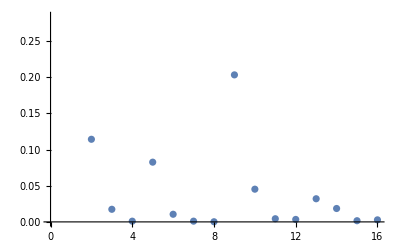

```mathematica
ListPlot[%282]
```